## Coordinate Free Expressions of Exponentials of Multivectors in Cl(p, q) for p + q = 3

Authors: A. Acus and A. Dargys , 2021-07-16
Load package. Wait until evaluation of cell is finished to be sure that no errors were produced.

## Exponent of multivector

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"GA.nb"}]]
```

### Exponent of Cl(0,3)

Define basis

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"CoordinateFree"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

```mathematica
D[gaPE[expFormExactRezultForSeries]/.a[x_]:>(t*a[x]),t]/.t->1
```

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[gaPE[expFormExactRezultForSeries]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030

```mathematica
gaDeterminantOfMV[gaGeneralMultivector[a,testAlgebra,{1,2}]]//Factor//FullSimplify
```

((a[3]-a[4])^2+(a[2]+a[5])^2+(a[1]-a[6])^2) ((a[3]+a[4])^2+(a[2]-a[5])^2+(a[1]+a[6])^2)

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+2608+1/24 a[3] a[4] a[7]^4 123030-1/24 a[2] a[5] a[7]^4 123030+1/24 a[1] a[6] a[7]^4 123030+1/120 a[7]^5 123030+1/120 a[0] a[7]^5 123030
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+2608+1/24 a[3] a[4] a[7]^4 123030-1/24 a[2] a[5] a[7]^4 123030+1/24 a[1] a[6] a[7]^4 123030+1/120 a[7]^5 123030+1/120 a[0] a[7]^5 123030
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→10,a[1]→-9,a[2]→9,a[3]→9,a[4]→0,a[5]→2,a[6]→-2,a[7]→0}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

```mathematica
theMV=testMV/.rndReplRules
```

10-9 1030+9 2030+9 3030+2 13030-2 23030

```mathematica
theMVExp=gaExponentOfMV[theMV]
```

1/2 ⅇ^10 ((1-123030)\[GeometricProduct](Cos[√251]+(Sin[√251] (-9 1030+9 2030+9 3030+2 13030-2 23030))/(√251))+(1+123030)\[GeometricProduct](Cos[√251]+(Sin[√251] (-9 1030+9 2030+9 3030+2 13030-2 23030))/(√251)))

```mathematica
Collect[gaPE[theMVExp],_𝕖,Simplify]
```

ⅇ^10 Cos[√251]-(9 ⅇ^10 Sin[√251] 1030)/(√251)+(9 ⅇ^10 Sin[√251] 2030)/(√251)+(9 ⅇ^10 Sin[√251] 3030)/(√251)+(2 ⅇ^10 Sin[√251] 13030)/(√251)-(2 ⅇ^10 Sin[√251] 23030)/(√251)

Numerical tests. It is important to take MV series of which is convergent (can be avoided for exp)

```mathematica
maxCoeff=gaNormDeterminant[testMV/.rndReplRules]+1
```

1+3 √39

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

1.15309-0.678228 1030+0.678228 2030+0.678228 3030+0.150717 13030-0.150717 23030

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

1.15309-0.678228 1030+0.678228 2030+0.678228 3030+0.150717 13030-0.150717 23030

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

1.15309-0.678228 1030+0.678228 2030+0.678228 3030+0.150717 13030-0.150717 23030

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1/2 ((1-123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))), √(a[4]^2+a[5]^2+a[6]^2)≠0}, {1/2 ((1-123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)+(1+123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)), True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2-a[5]^2-a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2+a[5]^2+a[6]^2

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))), √(a[4]^2+a[5]^2+a[6]^2)≠0}, {1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)+(1+123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)), True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1030+a[2] 2030+a[3] 3030))/(√(a[1]^2+a[2]^2+a[3]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1030+a[2] 2030+a[3] 3030))/(√(a[1]^2+a[2]^2+a[3]^2)))), √(a[1]^2+a[2]^2+a[3]^2)≠0}, {1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](1+a[1] 1030+a[2] 2030+a[3] 3030)+(1+123030)\[GeometricProduct](1+a[1] 1030+a[2] 2030+a[3] 3030)), True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}]//gaPE
```

-a[1]^2-a[2]^2-a[3]^2

scalar + Pseudoscalar

```mathematica
expFormExactRezultScalarPseudoscalar=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,3}]]//FullSimplify
```

ⅇ^a[0] (Cosh[a[7]]+Sinh[a[7]] 123030)

#### Example 1

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

```mathematica
ex1=gaRandomMultivector[testAlgebra]
```

```mathematica
ex1=-8-6 𝕖[2]-9 𝕖[3]+5 𝕖[1,2]-5 𝕖[1,3]+6 𝕖[2,3]-4 𝕖[1,2,3]
```

```mathematica
gaNormDeterminant[ex1]//N
```

```mathematica
listOfa12=#[[5]]&/@((gaGetMVComponents/@Table[Expand[gaPE[gaGeometricProductSeries[Exp[#]&,{ex1,{0,i}}]//Normal]]//N,{i,1,60}])/.{_𝕖->1})
```

```mathematica
ListPlot[listOfa12,AxesLabel->{"Number of sum terms","Value of coefficient at 𝕖[1,2]"},PlotRange->All,Joined->True]
```

```mathematica
Expand[gaPE[gaGeometricProductSeries[Exp[#]&,{ex1,{0,50}}]//Normal]]//N
```

```mathematica
answ1=gaExponentOfMV[ex1]//gaPE//Expand//N
```

Stop the example demo here

```mathematica
ex2=ex1/Max[Abs[(gaGetMVComponents[ex1]/.{_𝕖->1})]]
```

1/9 (-8+8 1300-3 2300+7 3300+3 12300+9 13300+7 23300+3 123300)

```mathematica
ex2Exp=Collect[gaPE[gaExponentOfMV[ex2]],_𝕖]//N
```

0.0807057+0.0440336 1300+0.184728 2300+0.137177 3300+0.320346 12300+0.39283 13300+0.484415 23300+0.557138 123300

```mathematica
Expand[gaPE[GeometricProduct@@Table[ex2Exp,{Max[Abs[(gaGetMVComponents[ex1]/.{_𝕖->1})]]}]]]
```

1.4732+1.28339 1300-0.179442 2300+1.27092 3300+0.936976 12300+1.9587 13300+1.79173 23300+2.60778 123300

```mathematica
listOfa12MaxCoeff=#[[5]]&/@((gaGetMVComponents/@Table[Expand[gaPE[gaGeometricProductSeries[Exp[#]&,{ex2,{0,i}}]//Normal]]//N,{i,1,60}])/.{_𝕖->1})
```

{0.333333,0.296296,0.500229,0.233145,0.342797,0.314316,0.321492,0.320347,0.320288,0.320365,0.320342,0.320347,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346,0.320346}

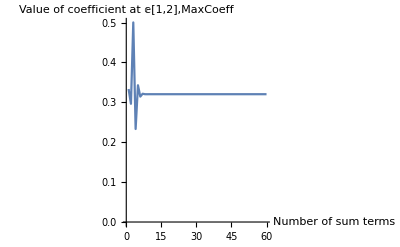

```mathematica
ListPlot[listOfa12MaxCoeff,AxesLabel->{"Number of sum terms","Value of coefficient at 𝕖[1,2],MaxCoeff"},PlotRange->All,Joined->True]
```

```mathematica
ex3=ex1/Ceiling[gaNormDeterminant[ex1]]
```

1/17 (-8+8 1300-3 2300+7 3300+3 12300+9 13300+7 23300+3 123300)

```mathematica
ex3Exp=Collect[gaPE[gaExponentOfMV[ex3]],_𝕖]//N
```

0.544726+0.204464 1300-0.00864874 2300+0.212252 3300+0.179379 12300+0.346065 13300+0.329628 23300+0.322908 123300

```mathematica
Expand[gaPE[GeometricProduct@@Table[ex3Exp,{Ceiling[gaNormDeterminant[ex1]]}]]]
```

1.4732+1.28339 1300-0.179442 2300+1.27092 3300+0.936976 12300+1.9587 13300+1.79173 23300+2.60778 123300

```mathematica
listOfa12DetNorm=#[[5]]&/@((gaGetMVComponents/@Table[Expand[gaPE[gaGeometricProductSeries[Exp[#]&,{ex3,{0,i}}]//Normal]]//N,{i,1,50}])/.{_𝕖->1})
```

{0.176471,0.16609,0.19635,0.175369,0.179929,0.179302,0.179386,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379,0.179379}

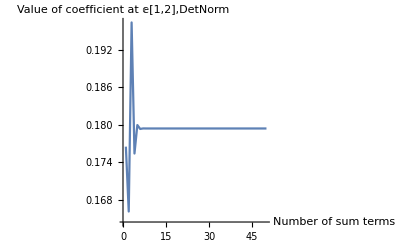

```mathematica
ListPlot[listOfa12DetNorm,AxesLabel->{"Number of sum terms","Value of coefficient at 𝕖[1,2],DetNorm"},PlotRange->All,Joined->True]
```

### Exponent of Cl(3,0)

Define basis

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

#### Proof [takes 20 min to compute, not suitable for real time demo]

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
(*expFormExactRezultForSeries=FullSimplify[#,Assumptions->Element[{a[0],a[1],a[2],a[3],a[4],a[5],a[6],a[7]},Reals]]&/@expFormExactRezult[[1,1,1]]*)expFormExactRezultForSeries=Collect[expFormExactRezult[[1,1,1]],_𝕖,FullSimplify[#,Assumptions->Element[{a[0],a[1],a[2],a[3],a[4],a[5],a[6],a[7]},Reals]]&]
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]-Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)])+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 1300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[2] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[5] (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (-a[1]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 2300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 3300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 12300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (-a[1]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[2] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[5] (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 13300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 23300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[a[7]]+Cos[a[7]] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 123300

Takes a bit to compute

```mathematica
(collectedAnswer=Collect[(Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)]),_𝕖,Together])
```

0

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→3,a[1]→10,a[2]→1,a[3]→0,a[4]→6,a[5]→-10,a[6]→-10,a[7]→-4}

```mathematica
(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)/.rndReplRules//N
```

152870.+119008. 1300-107865. 2300-65326.6 3300+6078.14 12300-21018. 13300+98747.5 23300+59446. 123300

```mathematica
Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]]/.rndReplRules//N
```

152870.+119008. 1300-107865. 2300-65326.6 3300+6078.14 12300-21018. 13300+98747.5 23300+59446. 123300

#### Tests & Examples

General case

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

6

```mathematica
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}][[1,1,1]]
```

ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]-Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)])+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]-((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 1300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 2300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]-((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 3300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 12300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (-Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 13300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 23300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[a[7]]+Cos[a[7]] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 123300

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+2586+1/12 a[4]^2 a[7]^3 123300+1/12 a[0] a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[0] a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/12 a[0] a[6]^2 a[7]^3 123300+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[7]^5 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult
```

ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]-Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)])+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]-((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 1300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 2300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]-((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 3300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 12300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (-Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 13300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-(a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Cos[a[7]]+((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)) Sin[a[7]]) Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 23300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cosh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)] Sin[a[7]]+Cos[a[7]] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sinh[(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2)]) 123300

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+15201+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[7]^5 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-10,a[1]→9,a[2]→-7,a[3]→9,a[4]→-6,a[5]→-3,a[6]→-10,a[7]→10}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests. It is important to take MV series of which is convergent

```mathematica
maxCoeff=gaNormDeterminant[testMV/.rndReplRules]+1
```

1+2^(3/4) 2657^(1/4)

```mathematica
(gpSeriesAnswerNC=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,20}},Expand->Automatic]//Normal//Expand)//N
```

0.67681+0.482076 1300-0.294062 2300+0.414357 3300-0.0561512 12300+0.0142488 13300-0.195164 23300-0.00731491 123300

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.67681+0.482076 1300-0.294062 2300+0.414357 3300-0.0561512 12300+0.0142488 13300-0.195164 23300-0.00731491 123300

```mathematica
(expFormExactRezultSeriesNC=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,20}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,20}]})]/.{α->1}])//N//Chop
```

0.67681+0.482076 1300-0.294062 2300+0.414357 3300-0.0561512 12300+0.0142488 13300-0.195164 23300-0.00731491 123300

Takes 2 min to finish, leave unevaluated

```mathematica
formalDifferenceNC=Collect[expFormExactRezultSeriesNC-gpSeriesAnswerNC//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests. Without division

```mathematica
gaExponentOfMV[(testMV)/.rndReplRules]//gaPE//Expand//N
```

-1.96235-5.05336 1300-3.00998 2300+0.757183 3300-19.3891 12300-13.3261 13300-23.5993 23300-32.8501 123300

```mathematica
(gpSeriesAnswerNC=Table[(gaGeometricProductSeries[Exp[#]&,{(testMV)/.rndReplRules,{0,step}},Expand->Automatic]//Normal//Expand)//N,{step,10,90,10}])
```

{5.37052×10^7-2.43338×10^7 1300+3.66691×10^7 2300-3.91882×10^7 3300+7.44024×10^7 12300+4.64852×10^7 13300+1.01722×10^8 23300-1.32121×10^8 123300,-1.51751×10^11+1.28492×10^11 1300-4.12165×10^10 2300+7.93297×10^10 3300+1.06891×10^11 12300+8.41723×10^10 13300+1.04409×10^11 23300-1.67147×10^11 123300,-2.18339×10^12+1.52013×10^12 1300-9.36283×10^11 2300+1.31414×10^12 3300-2.06634×10^11 12300+2.54255×10^10 13300-6.53372×10^11 23300+5.68361×10^11 123300,-2.01195×10^11+5.83432×10^10 1300-1.71654×10^11 2300+1.64062×10^11 3300-4.52962×10^11 12300-2.92555×10^11 13300-5.96358×10^11 23300+7.91896×10^11 123300,1.79198×10^10-1.48956×10^10 1300+5.15717×10^9 2300-9.51377×10^9 3300-1.11484×10^10 12300-8.93786×10^9 13300-1.0508×10^10 23300+1.72256×10^10 123300,1.00472×10^8-6.96574×10^7 1300+4.33917×10^7 2300-6.0627×10^7 3300+1.10694×10^7 12300-109287. 13300+3.19945×10^7 23300-2.88141×10^7 123300,21145.7-6292.94 1300+17877.2 2300-17162.2 3300+46766.4 12300+30176.5 13300+61640.1 23300-81863. 123300,-13.6689+4.73885 1300-6.31498 2300+6.94005 3300-11.7806 12300-7.26604 13300-16.3325 23300-44.6579 123300,-1.96327-5.05272 1300-3.01037 2300+0.757737 3300-19.3891 12300-13.3261 13300-23.5996 23300-32.8499 123300}

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1, Positive[-a[4]^2-a[5]^2-a[6]^2]||(!Negative[-a[4]^2-a[5]^2-a[6]^2]&&a[4]^2+a[5]^2+a[6]^2==0)}, {Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2)), Negative[-a[4]^2-a[5]^2-a[6]^2]}, {0, True}}]

Rotor

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2-a[5]^2-a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2+a[5]^2+a[6]^2

```mathematica
expFormExactRezultRotor=gaExponentOfMV[φ*gaGeneralMultivector[a,testAlgebra,{2}]/Sqrt[(gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE)]]//FullSimplify
```

Piecewise[{{1, Positive[-φ^2]||φ==0}, {Cos[φ]+(Sin[φ] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2)), Negative[-φ^2]}, {0, True}}]

Bivector +scalar=rotor when normalized

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1, Positive[-a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0] (Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2))), Negative[-a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0], a[4]^2+a[5]^2+a[6]^2==0}, {0, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2+a[3]^2)]-(123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct]123300 Sinh[√(a[1]^2+a[2]^2+a[3]^2)])/(√(a[1]^2+a[2]^2+a[3]^2))), Positive[a[1]^2+a[2]^2+a[3]^2]}, {1, Negative[a[1]^2+a[2]^2+a[3]^2]}, {ⅇ^a[0], a[1]^2+a[2]^2+a[3]^2==0}, {0, True}}]

#### Chappell Functions of multivector variables check

General case

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

6

```mathematica
chappelExp[exp_]:=Module[{a=gaGetMV[exp,{0}],v=gaGetMV[exp,{1}],jw=gaPE[-I*gaI[Cl[3,0]]\[GeometricProduct]gaGetMV[exp,{2}]],jt=gaGetMV[exp,{3}],fModule,fCapital},fCapital=(v+jw);fModule=Sqrt[gaPE[-v\[GeometricProduct]v-jw\[GeometricProduct]jw-2v\[InnerProduct]jw]];
Exp[a+-I*gaPE[jt\[GeometricProduct]gaI[Cl[3,0]]]]*(Cos[fModule]+(fCapital/fModule)*Sin[fModule])
]
```

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-6,a[1]→-9,a[2]→-4,a[3]→-5,a[4]→9,a[5]→-6,a[6]→1,a[7]→-1}

```mathematica
((chappelExp[testMV]/.rndReplRules//ComplexExpand//Expand)//.Complex[a_,b_]:>(a+gaI[Cl[3,0]]*b)/.Times->GeometricProduct)//gaPE//Expand//N
```

-9.10254+6.43496 1300+4.80626 2300+6.53332 3300-4.33298 12300+2.6551 13300+2.4769 23300+2.76089 123300

```mathematica
gaExponentOfMV[testMV]/.rndReplRules//gaPE//Expand//N
```

-9.10254+6.43496 1300+4.80626 2300+6.53332 3300-4.33298 12300+2.6551 13300+2.4769 23300+2.76089 123300

### Exponent of Cl(2,1)

Define basis

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{1,1210,2210,3210,12210,13210,23210,123210}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,1,1]]
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,2,1]]
```

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,3,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]+ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,4,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]+ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 3210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 12210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 23210+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]) 123210

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

1/2 ⅇ^a[0] a[0] (ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]-(ⅇ^(-a[7]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 √(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)))+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[1]+a[6]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[2]-a[5]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[3]-a[4]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[3]-a[4]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[2]-a[5]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-((ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)))+(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[1]+a[6]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] a[0] (-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210+1/2 ⅇ^a[0] (ⅇ^(-a[7]) a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]+(ⅇ^(-a[7]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 √(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 123210

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+2491+1/12 a[0] a[1]^2 a[7]^3 123210+1/12 a[2]^2 a[7]^3 123210+1/12 a[0] a[2]^2 a[7]^3 123210-1/12 a[3]^2 a[7]^3 123210-1/12 a[0] a[3]^2 a[7]^3 123210-1/12 a[4]^2 a[7]^3 123210-1/12 a[0] a[4]^2 a[7]^3 123210+1/12 a[5]^2 a[7]^3 123210+1/12 a[0] a[5]^2 a[7]^3 123210+1/12 a[6]^2 a[7]^3 123210+1/12 a[0] a[6]^2 a[7]^3 123210+1/24 a[3] a[4] a[7]^4 123210-1/24 a[2] a[5] a[7]^4 123210+1/24 a[1] a[6] a[7]^4 123210+1/120 a[7]^5 123210+1/120 a[0] a[7]^5 123210
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+2491+1/12 a[0] a[1]^2 a[7]^3 123210+1/12 a[2]^2 a[7]^3 123210+1/12 a[0] a[2]^2 a[7]^3 123210-1/12 a[3]^2 a[7]^3 123210-1/12 a[0] a[3]^2 a[7]^3 123210-1/12 a[4]^2 a[7]^3 123210-1/12 a[0] a[4]^2 a[7]^3 123210+1/12 a[5]^2 a[7]^3 123210+1/12 a[0] a[5]^2 a[7]^3 123210+1/12 a[6]^2 a[7]^3 123210+1/12 a[0] a[6]^2 a[7]^3 123210+1/24 a[3] a[4] a[7]^4 123210-1/24 a[2] a[5] a[7]^4 123210+1/24 a[1] a[6] a[7]^4 123210+1/120 a[7]^5 123210+1/120 a[0] a[7]^5 123210
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-7,a[1]→-3,a[2]→-10,a[3]→8,a[4]→3,a[5]→-7,a[6]→8,a[7]→9}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.Special cases. When (a+)^2=0, the conditions applies a3-a12=0;a2-a13=0; a1+a23=0, i.𝕖. a3-a4=0;a2-a5=0; a1+a6=0

```mathematica
rndReplRulesIndep=(((a[#]->RandomInteger[{-10,10}])&/@Range[0,7])/.{(a[4|5|6]->_)->Nothing});
rndReplRules=Flatten[{{a[4]->a[3],a[5]->a[2],a[6]->-a[1]}/.rndReplRulesIndep,rndReplRulesIndep}]
```

{a[4]→3,a[5]→-10,a[6]→-9,a[0]→5,a[1]→9,a[2]→-10,a[3]→3,a[7]→10}

```mathematica
maxCoeff=gaNormDeterminant[testMV/.rndReplRules]+1
```

1+3^(3/4) √5 221^(1/4)

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

1.78764+0.441744 1210-0.490826 2210+0.147248 3210+0.147248 12210-0.490826 13210-0.441744 23210+0.279769 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand
```

1/2 ⅇ^(15/(1+3^(3/4) √5 221^(1/4)))+1/2 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Cosh[(4 √43)/(1+3^(3/4) √5 221^(1/4))]+(9 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 1210)/(4 √43 (1+3^(3/4) √5 221^(1/4)))+(9 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 1210)/(4 (1+3^(3/4) √5 221^(1/4)))-(5 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 2210)/(2 √43 (1+3^(3/4) √5 221^(1/4)))-(5 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 2210)/(2 (1+3^(3/4) √5 221^(1/4)))+(3 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 3210)/(4 √43 (1+3^(3/4) √5 221^(1/4)))+(3 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 3210)/(4 (1+3^(3/4) √5 221^(1/4)))+(3 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 12210)/(4 √43 (1+3^(3/4) √5 221^(1/4)))+(3 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 12210)/(4 (1+3^(3/4) √5 221^(1/4)))-(5 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 13210)/(2 √43 (1+3^(3/4) √5 221^(1/4)))-(5 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 13210)/(2 (1+3^(3/4) √5 221^(1/4)))-(9 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 23210)/(4 √43 (1+3^(3/4) √5 221^(1/4)))-(9 √(5/43) 3^(3/4) 221^(1/4) ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Sinh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 23210)/(4 (1+3^(3/4) √5 221^(1/4)))+1/2 ⅇ^(15/(1+3^(3/4) √5 221^(1/4))) 123210-1/2 ⅇ^(-5/(1+3^(3/4) √5 221^(1/4))) Cosh[(4 √43)/(1+3^(3/4) √5 221^(1/4))] 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

1.78764+0.441744 1210-0.490827 2210+0.147248 3210+0.147248 12210-0.490827 13210-0.441744 23210+0.27977 123210

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

1.78764+0.441744 1210-0.490826 2210+0.147248 3210+0.147248 12210-0.490826 13210-0.441744 23210+0.279769 123210

Numerical tests.Special cases. When (a-)^2=0, the conditions applies a3+a12=0;a2+a13=0; a1-a23=0, i.𝕖. a3+a4=0;a2+a5=0; a1-a6=0

```mathematica
rndReplRulesIndep=(((a[#]->RandomInteger[{-10,10}])&/@Range[0,7])/.{(a[4|5|6]->_)->Nothing});
rndReplRules=Flatten[{{a[4]->-a[3],a[5]->-a[2],a[6]->a[1]}/.rndReplRulesIndep,rndReplRulesIndep}]
```

{a[4]→1,a[5]→-10,a[6]→7,a[0]→5,a[1]→7,a[2]→10,a[3]→-1,a[7]→-2}

```mathematica
maxCoeff=gaNormDeterminant[testMV/.rndReplRules]+1
```

1+√7 583^(1/4)

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

2.63972+0.981863 1210+1.40266 2210-0.140266 3210+0.140266 12210-1.40266 13210+0.981863 23210+0.991037 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

2.63973+0.98187 1210+1.40267 2210-0.140267 3210+0.140267 12210-1.40267 13210+0.98187 23210+0.991048 123210

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

2.63972+0.981863 1210+1.40266 2210-0.140266 3210+0.140266 12210-1.40266 13210+0.981863 23210+0.991037 123210

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1/2 ((1-123210)\[GeometricProduct](Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2)))+(1+123210)\[GeometricProduct](Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2)))), Positive[a[4]^2-a[5]^2-a[6]^2]}, {1/2 ((1-123210)\[GeometricProduct](Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2)))+(1+123210)\[GeometricProduct](Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2)))), Negative[a[4]^2-a[5]^2-a[6]^2]}, {1/2 ((1-123210)\[GeometricProduct](1+a[4] 12210+a[5] 13210+a[6] 23210)+(1+123210)\[GeometricProduct](1+a[4] 12210+a[5] 13210+a[6] 23210)), a[4]^2==a[5]^2+a[6]^2}, {0, True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2+a[5]^2+a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2-a[5]^2-a[6]^2

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2)))+(1+123210)\[GeometricProduct](Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2)))), Positive[a[4]^2-a[5]^2-a[6]^2]}, {1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2)))+(1+123210)\[GeometricProduct](Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2)))), Negative[a[4]^2-a[5]^2-a[6]^2]}, {1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](1+a[4] 12210+a[5] 13210+a[6] 23210)+(1+123210)\[GeometricProduct](1+a[4] 12210+a[5] 13210+a[6] 23210)), a[4]^2==a[5]^2+a[6]^2}, {0, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(-a[1]^2-a[2]^2+a[3]^2)))+(1+123210)\[GeometricProduct](Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(-a[1]^2-a[2]^2+a[3]^2)))), Positive[-a[1]^2-a[2]^2+a[3]^2]}, {1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](Cosh[√(a[1]^2+a[2]^2-a[3]^2)]+(Sinh[√(a[1]^2+a[2]^2-a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(a[1]^2+a[2]^2-a[3]^2)))+(1+123210)\[GeometricProduct](Cosh[√(a[1]^2+a[2]^2-a[3]^2)]+(Sinh[√(a[1]^2+a[2]^2-a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(a[1]^2+a[2]^2-a[3]^2)))), Negative[-a[1]^2-a[2]^2+a[3]^2]}, {1/2 ⅇ^a[0] ((1-123210)\[GeometricProduct](1+a[1] 1210+a[2] 2210+a[3] 3210)+(1+123210)\[GeometricProduct](1+a[1] 1210+a[2] 2210+a[3] 3210)), a[1]^2+a[2]^2==a[3]^2}, {0, True}}]

scalar + Pseudoscalar

```mathematica
expFormExactRezultScalarPseudoscalar=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,3}]]//FullSimplify
```

ⅇ^a[0] (Cosh[a[7]]+Sinh[a[7]] 123210)

### Hyperbolic trigonometric functions in Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

Check that -A in exponent yields inverse (when multiplied by either side)

```mathematica
Collect[gaExponentOfMV[-testMV][[1,1,1]]\[GeometricProduct]gaExponentOfMV[testMV][[1,1,1]]//gaPE//Expand,_𝕖,ExpandAll[Simplify[Together[#]]]&]
```

1

```mathematica
Collect[gaExponentOfMV[testMV][[1,1,1]]\[GeometricProduct]gaExponentOfMV[-testMV][[1,1,1]]//gaPE//Expand,_𝕖,ExpandAll[Simplify[Together[#]]]&]
```

1

#### Sinh tests

Sinh: general case, replace complex expressions to simpler

```mathematica
rules2aSaI={2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]->aI,(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)->aS};rules2aPaR={aI/(√2 √(aS+√(aI^2+aS^2)))->aP,aI^2/(2 (aS+√(aI^2+aS^2)))->aP^2,(√(aS+√(aI^2+aS^2)))/(√2)->aR,1/2 (aS+√(aI^2+aS^2))->aR^2};
```

```mathematica
gaSinhOfMVx=((1/2)*(gaExponentOfMV[testMV][[1,1,1]]-gaExponentOfMV[-testMV][[1,1,1]])//.rules2aSaI)//.rules2aPaR
```

1/2 (-ⅇ^(-a[0]) ((Cos[a[7]]-Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300)+aP (-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300))+ⅇ^a[0] ((Cos[a[7]]+Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300)+aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300)))

```mathematica
gaSinhOfMVSimplified=Collect[gaPE[(((gaExponentOfMV[testMV][[1,1,1]]-gaExponentOfMV[-testMV][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR],_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

-Cosh[a[0]] Sin[aP] Sin[a[7]] Sinh[aR]+Cos[aP] Cos[a[7]] Cosh[aR] Sinh[a[0]]+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 1300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR])+Sin[a[7]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 2300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 3300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR])+Sin[a[7]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 12300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 13300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR])+Sin[a[7]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 23300+(Cos[aP] Cosh[aR] Cosh[a[0]] Sin[a[7]]+Cos[a[7]] Sin[aP] Sinh[aR] Sinh[a[0]]) 123300

Check if series expansions coincide

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Sinh[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

a[0]+a[0]^3/6+a[0]^5/120+1/2 a[0] a[1]^2+1/12 a[0]^3 a[1]^2+1/24 a[0] a[1]^4+1/2 a[0] a[2]^2+1/12 a[0]^3 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0] a[2]^4+1/2 a[0] a[3]^2+1/12 a[0]^3 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+844+1/12 a[4]^2 a[6]^2 a[7] 123300+1/12 a[5]^2 a[6]^2 a[7] 123300+1/24 a[6]^4 a[7] 123300-1/2 a[0] a[3] a[4] a[7]^2 123300+1/2 a[0] a[2] a[5] a[7]^2 123300-1/2 a[0] a[1] a[6] a[7]^2 123300-1/6 a[7]^3 123300-1/12 a[0]^2 a[7]^3 123300-1/12 a[1]^2 a[7]^3 123300-1/12 a[2]^2 a[7]^3 123300-1/12 a[3]^2 a[7]^3 123300+1/12 a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/120 a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(sinhFormExactRezultForSeries=(gaSinhOfMVSimplified/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))//LeafCount
```

12165

```mathematica
sinhFormExactRezultSeries=Normal[(sinhFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

a[0]+a[0]^3/6+a[0]^5/120+5718+(a[1]^2 a[6]^2 a[7]^3 123300)/(6 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/120 a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[sinhFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

```mathematica
rndReplRulesForArticleExample={a[0]->4,a[1]->1,a[2]->3,a[3]->-5,a[4]->10,a[5]->9,a[6]->-9,a[7]->-4}
```

{a[0]→4,a[1]→1,a[2]→3,a[3]→-5,a[4]→10,a[5]→9,a[6]→-9,a[7]→-4}

```mathematica
rndReplRules=rndReplRulesForArticleExample;
gaGeneralMultivector[a,testAlgebra]/.rndReplRulesForArticleExample
```

4+1300+3 2300-5 3300+10 12300+9 13300-9 23300-4 123300

```mathematica
gaDeterminantOfMV[testMV/.rndReplRules]
```

71129

```mathematica
gaNormDeterminant[testMV/.rndReplRules]//N
```

16.331

```mathematica
maxCoeff=(gaNormDeterminant[testMV/.rndReplRules]//Ceiling)
```

17

```mathematica
(gpSeriesSinhAnswerNC6=gaGeometricProductSeries[Sinh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.080657-0.0229634 1300+0.0788338 2300-0.172424 3300+0.55002 12300+0.482708 13300-0.466294 23300-0.207635 123300

```mathematica
(gpSeriesSinhAnswerNC40=gaGeometricProductSeries[Sinh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.0806083-0.0230641 1300+0.0787983 2300-0.172439 3300+0.550421 12300+0.483046 13300-0.466603 23300-0.208249 123300

```mathematica
(gaSinhOfMVN=(gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]-gaExponentOfMV[-(testMV/maxCoeff)/.rndReplRules])/2//gaPE//Expand)//N
```

0.0806083-0.0230641 1300+0.0787983 2300-0.172439 3300+0.550421 12300+0.483046 13300-0.466603 23300-0.208249 123300

So, 20 series terms yields 6 digit match. To see difference reduce expansion order

#### Cosh tests

Do same computations for cosh

```mathematica
gaCoshOfMVx=((1/2)*(gaExponentOfMV[testMV][[1,1,1]]+gaExponentOfMV[-testMV][[1,1,1]])//.rules2aSaI)//.rules2aPaR
```

1/2 (ⅇ^(-a[0]) ((Cos[a[7]]-Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300)+aP (-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300))+ⅇ^a[0] ((Cos[a[7]]+Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300)+aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300)))

```mathematica
gaCoshOfMVSimplified=Collect[(((gaExponentOfMV[testMV][[1,1,1]]+gaExponentOfMV[-testMV][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

1/2 (ⅇ^(-a[0]) ((Cos[a[7]]-Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300)-aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300))+ⅇ^a[0] ((Cos[a[7]]+Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300)+aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300)))

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Cosh[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]^2/2+a[0]^4/24+a[0]^6/720+a[1]^2/2+1/4 a[0]^2 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[2]^2/2+1/4 a[0]^2 a[2]^2+1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2+1700+1/12 a[1] a[6]^3 a[7]^2 123300-1/6 a[0] a[7]^3 123300-1/36 a[0]^3 a[7]^3 123300-1/12 a[0] a[1]^2 a[7]^3 123300-1/12 a[0] a[2]^2 a[7]^3 123300-1/12 a[0] a[3]^2 a[7]^3 123300+1/12 a[0] a[4]^2 a[7]^3 123300+1/12 a[0] a[5]^2 a[7]^3 123300+1/12 a[0] a[6]^2 a[7]^3 123300+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

Back substitute

```mathematica
(coshFormExactRezultForSeries=gaPE[(gaCoshOfMVSimplified/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI)])//LeafCount
```

8682

```mathematica
coshFormExactRezultSeries=Normal[(coshFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]^2/2+a[0]^4/24+a[0]^6/720+a[1]^2/4+9701+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

```mathematica
formalDifference=Collect[coshFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

We will use the same random numerical coefficients, since we want to do same computations with tanh/ctanh later

```mathematica
(gpSeriesCoshAnswerNC6=gaGeometricProductSeries[Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.604072-0.11113 1300-0.0900395 2300+0.0824682 3300+0.173052 12300+0.135467 13300-0.108428 23300-0.293931 123300

```mathematica
(gpSeriesCoshAnswerNC40=gaGeometricProductSeries[Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.603979-0.111183 1300-0.0900923 2300+0.0825266 3300+0.173083 12300+0.135487 13300-0.108436 23300-0.293965 123300

```mathematica
(gaCoshOfMVN=(gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]+gaExponentOfMV[-(testMV/maxCoeff)/.rndReplRules])/2//gaPE//Expand)//N
```

0.603979-0.111183 1300-0.0900923 2300+0.0825266 3300+0.173083 12300+0.135487 13300-0.108436 23300-0.293965 123300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVN,gaSinhOfMVN]]//N
```

0.

So, 20 series terms yields 6 digit match. To see difference reduce expansion order

#### Tanh tests

First, show that sinh and cosh commutes. In fact ANY two continuous functions of the same MV commute, since any finite order expansions contains the same MV.  In this particular case this follows also from exponential form.

```mathematica
(gaSinhOfMVSimplified\[GeometricProduct]gaCoshOfMVSimplified-gaCoshOfMVSimplified\[GeometricProduct]gaSinhOfMVSimplified)//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaSinhOfMVSimplified,gaCoshOfMVSimplified]]//gaPE//Expand
```

0

Since they commute, we can compute cosh inverse: the answer is quite large

```mathematica
(gaCoshOfMVInv=gaInverse[gaCoshOfMVSimplified,Method->"Involutions",Expand->(Expand[gaPE[#]]&)])//LeafCount
```

1063114

Check for safety, that it also commutes both with sing and cosh

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVInv,gaPE[gaCoshOfMVSimplified]]]
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVInv,gaPE[gaSinhOfMVSimplified]]]
```

0

Since expressions are large, comparison of series expansion is challenging, therefore we will test numerically. First exact formulas (with multiplication terms interchanged). Note, that original symbolical coefficients are replaced by dividing them by /maxCoeff. First check that inversion is computed correctly

```mathematica
((gaPE[(gaCoshOfMVSimplified\[GeometricProduct]gaCoshOfMVInv)]/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.+2.44664×10^-17 1300+1.7677×10^-15 2300+5.50495×10^-17 3300+2.26315×10^-16 12300+1.10099×10^-15 13300+4.89329×10^-17 23300+5.26028×10^-16 123300

```mathematica
((gaPE[(gaCoshOfMVInv\[GeometricProduct]gaCoshOfMVSimplified)]/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.-3.64631×10^-17 1300-4.86175×10^-17 2300-4.86175×10^-17 3300+2.43087×10^-17 12300-1.64084×10^-16 13300-1.82316×10^-17 23300+7.29262×10^-17 123300

```mathematica
(gaCoshOfMVInvN=Expand[((gaCoshOfMVInv/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])])//N
```

1.11062-0.0432608 1300-0.107624 2300+0.173218 3300-0.315659 12300-0.28594 13300+0.288402 23300+0.597881 123300

```mathematica
(gpSeriesCoshInvAnswerNC6=gaGeometricProductSeries[1/Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

1.18909+0.0173437 1300-0.0624098 2300+0.135806 3300-0.430557 12300-0.377964 13300+0.365249 23300+0.759489 123300

```mathematica
(gpSeriesCoshInvAnswerNC40=gaGeometricProductSeries[1/Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

1.11035-0.0434127 1300-0.107776 2300+0.173387 3300-0.315576 12300-0.28589 13300+0.288386 23300+0.597792 123300

So, precision of numerical inverse check is very high. Now tanh. Note, that, since N is applied before expansion, the exact expressions are converted to approximate, since otherwise expansion will take very long.

```mathematica
tanhFormExactRezultNr=Expand[gaPE[(gaSinhOfMVN//N)\[GeometricProduct](gaCoshOfMVInvN//N)]]
```

0.623118+0.309929 1300+0.427191 2300-0.572374 3300+0.446695 12300+0.443909 13300-0.499753 23300+0.0547346 123300

```mathematica
(tanhFormExactRezultNl=(Expand[gaPE[(gaCoshOfMVInvN//N)\[GeometricProduct](gaSinhOfMVN//N)]]))
```

0.623118+0.309929 1300+0.427191 2300-0.572374 3300+0.446695 12300+0.443909 13300-0.499753 23300+0.0547346 123300

Lastly tanh series. For tanh it is very important to divide by proper value (max coefficient of MV is not enough: it yields nonconvergent series!)

```mathematica
(gpSeriesTanhAnswerNC6=gaGeometricProductSeries[Tanh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.762932+0.361672 1300+0.502945 2300-0.676555 3300+0.544676 12300+0.538714 13300-0.603389 23300-0.117601 123300

So, we see very good coincidence. Note, however that with even 20 terms only 3 digits coincide. In order to have 6 coinciding digits we need to take nearly 40 series terms

```mathematica
(gpSeriesTanhAnswerNC40=gaGeometricProductSeries[Tanh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.62316+0.30999 1300+0.427215 2300-0.57237 3300+0.446467 12300+0.443717 13300-0.499579 23300+0.0550762 123300

### Ordinary trigonometric functions in Cl(3,0)

Ordinary trigonometric functions can be defined only for algebras for which I^2=-1, i.𝕖. only for cl(3,0) and isomorphic cl(1,2).

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

#### Sin tests

Sin: general case, replace complex expressions to simpler

```mathematica
rules2aSaI={-2 a[3] a[4]+2 a[2] a[5]-2 a[1] a[6]->-aI,2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]->aI,(-a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)->-aS,(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)->aS};rules2aPaR={aI/(√2 √(-aS+√(aI^2+aS^2)))->aPP,aI^2/(2 (-aS+√(aI^2+aS^2)))->aPP^2,(√(-aS+√(aI^2+aS^2)))/(√2)->aRR,1/2 (-aS+√(aI^2+aS^2))->aRR^2};
```

Use 1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x) and replace imaginary i by pseudoscalar

```mathematica
gaSinOfMVSimplified=Collect[(gaPE[gaI[testAlgebra]\[GeometricProduct]((-gaExponentOfMV[gaPE[testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]]+gaExponentOfMV[gaPE[-testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]])/2)]//.rules2aSaI)//.rules2aPaR,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

Cos[aPP] Cosh[aRR] Cosh[a[7]] Sin[a[0]]+Cos[a[0]] Sin[aPP] Sinh[aRR] Sinh[a[7]]+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 1300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 2300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 3300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 12300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 13300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 23300+(-Cosh[a[7]] Sin[aPP] Sin[a[0]] Sinh[aRR]+Cos[aPP] Cos[a[0]] Cosh[aRR] Sinh[a[7]]) 123300

Check if series expansions coincide.

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Sin[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

a[0]-a[0]^3/6+a[0]^5/120-1/2 a[0] a[1]^2+1/12 a[0]^3 a[1]^2+1/24 a[0] a[1]^4-1/2 a[0] a[2]^2+1/12 a[0]^3 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0] a[2]^4-1/2 a[0] a[3]^2+1/12 a[0]^3 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+1/24 a[0] a[3]^4+840+1/12 a[4]^2 a[6]^2 a[7] 123300+1/12 a[5]^2 a[6]^2 a[7] 123300+1/24 a[6]^4 a[7] 123300-1/2 a[0] a[3] a[4] a[7]^2 123300+1/2 a[0] a[2] a[5] a[7]^2 123300-1/2 a[0] a[1] a[6] a[7]^2 123300+1/6 a[7]^3 123300-1/12 a[0]^2 a[7]^3 123300-1/12 a[1]^2 a[7]^3 123300-1/12 a[2]^2 a[7]^3 123300-1/12 a[3]^2 a[7]^3 123300+1/12 a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/120 a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(sinFormExactRezultForSeries=(gaSinOfMVSimplified//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//LeafCount
```

12159

```mathematica
sinFormExactRezultSeries=Normal[(sinFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

a[0]-a[0]^3/6+5719+1/120 a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[sinFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→5,a[1]→3,a[2]→8,a[3]→4,a[4]→6,a[5]→-3,a[6]→-8,a[7]→-6}

```mathematica
rndReplRulesForArticleExample={a[0]->4,a[1]->1,a[2]->3,a[3]->-5,a[4]->10,a[5]->9,a[6]->-9,a[7]->-4}
```

{a[0]→4,a[1]→1,a[2]→3,a[3]→-5,a[4]→10,a[5]→9,a[6]→-9,a[7]→-4}

```mathematica
Series[Tan[x],{x,0,10}]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835+O[x]^11

```mathematica
rndReplRules=rndReplRulesForArticleExample;
gaGeneralMultivector[a,testAlgebra]/.rndReplRulesForArticleExample
```

4+1300+3 2300-5 3300+10 12300+9 13300-9 23300-4 123300

```mathematica
gaDeterminantOfMV[testMV/.rndReplRules]
```

71129

```mathematica
gaNormDeterminant[testMV/.rndReplRules]//N
```

16.331

```mathematica
maxCoeff=(gaNormDeterminant[testMV/.rndReplRules]//Ceiling)
```

17

```mathematica
(gpSeriesSinAnswerNC6=gaGeometricProductSeries[Sin[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.414194+0.156085 1300+0.288685 2300-0.431261 3300+0.613118 12300+0.566771 13300-0.586723 23300-0.24373 123300

```mathematica
(gaSinOfMVN=gaPE[gaI[testAlgebra]\[GeometricProduct]((-gaExponentOfMV[gaPE[((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]]+gaExponentOfMV[gaPE[-((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]])/2)]//Expand)//N
```

0.414222+0.156178 1300+0.288709 2300-0.431231 3300+0.612706 12300+0.566421 13300-0.586401 23300-0.243095 123300

So, 20 series terms yields 6 digit match. To see difference reduce expansion order.

#### Cos tests

Sin: general case, replace complex expressions to simpler

Use ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2 and replace imaginary i by pseudoscalar

```mathematica
gaCosOfMVSimplified=Collect[gaPE[(((gaExponentOfMV[gaPE[testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]]+gaExponentOfMV[gaPE[-testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR],_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

Cos[aPP] Cos[a[0]] Cosh[aRR] Cosh[a[7]]-Sin[aPP] Sin[a[0]] Sinh[aRR] Sinh[a[7]]+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 1300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 2300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 3300+1/(√(aI^2+aS^2))(Cosh[a[7]] Sin[a[0]] ((aRR a[3]-aPP a[4]) Cosh[aRR] Sin[aPP]-(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 12300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 13300+1/(√(aI^2+aS^2))(Cosh[a[7]] Sin[a[0]] ((aRR a[1]-aPP a[6]) Cosh[aRR] Sin[aPP]-(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 23300+(-Cos[a[0]] Cosh[a[7]] Sin[aPP] Sinh[aRR]-Cos[aPP] Cosh[aRR] Sin[a[0]] Sinh[a[7]]) 123300

Check if series expansions coincide.

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Cos[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1-a[0]^2/2+a[0]^4/24-a[0]^6/720-a[1]^2/2+1/4 a[0]^2 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24-1/48 a[0]^2 a[1]^4-a[1]^6/720-a[2]^2/2+1/4 a[0]^2 a[2]^2-1/48 a[0]^4 a[2]^2+1735+1/12 a[2] a[5] a[6]^2 a[7]^2 123300-1/12 a[1] a[6]^3 a[7]^2 123300-1/6 a[0] a[7]^3 123300+1/36 a[0]^3 a[7]^3 123300+1/12 a[0] a[1]^2 a[7]^3 123300+1/12 a[0] a[2]^2 a[7]^3 123300+1/12 a[0] a[3]^2 a[7]^3 123300-1/12 a[0] a[4]^2 a[7]^3 123300-1/12 a[0] a[5]^2 a[7]^3 123300-1/12 a[0] a[6]^2 a[7]^3 123300-1/24 a[3] a[4] a[7]^4 123300+1/24 a[2] a[5] a[7]^4 123300-1/24 a[1] a[6] a[7]^4 123300-1/120 a[0] a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(cosFormExactRezultForSeries=(gaCosOfMVSimplified//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//LeafCount
```

12165

```mathematica
cosFormExactRezultSeries=Normal[(cosFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1-a[0]^2/2+a[0]^4/24-a[0]^6/720-a[1]^2/4+10320+1/24 a[2] a[5] a[7]^4 123300-1/24 a[1] a[6] a[7]^4 123300-1/120 a[0] a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[cosFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Check that sin^2+cos^2==1 is satisfied

```mathematica
Collect[(((gaCosOfMVSimplified\[GeometricProduct]gaCosOfMVSimplified+gaSinOfMVSimplified\[GeometricProduct]gaSinOfMVSimplified-1//gaPE)//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
(gpSeriesCosAnswerNC6=gaGeometricProductSeries[Cos[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

1.38385+0.107554 1300+0.0727025 2300-0.0517374 3300-0.243693 12300-0.198493 13300+0.17072 23300+0.41533 123300

```mathematica
(gaCosOfMVN=gaPE[((gaExponentOfMV[gaPE[((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]]+gaExponentOfMV[gaPE[-((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]])/2)]//Expand)//N
```

1.38376+0.1075 1300+0.072649 2300-0.0516786 3300-0.243659 12300-0.198472 13300+0.170711 23300+0.415293 123300

So, 20 series terms yields 6 digit match. To see difference reduce expansion order.

#### Tan tests

First, show that sin and cos commutes. In fact ANY two continuous functions of the same MV commute, since any finite order expansions contains the same MV.  In this particular case this follows also from exponential form.

```mathematica
(gaSinOfMVSimplified\[GeometricProduct]gaCosOfMVSimplified-gaCosOfMVSimplified\[GeometricProduct]gaSinOfMVSimplified)//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaSinOfMVSimplified,gaCosOfMVSimplified]]
```

0

Since they commute, we can compute cosh inverse: the answer is quite large

```mathematica
(gaCosOfMVInv=gaInverse[gaCosOfMVSimplified,Method->"Involutions",Expand->(Expand[gaPE[#]]&)])//LeafCount
```

315952

Check for safety, that it also commutes both with sing and cosh

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCosOfMVInv,gaCosOfMVSimplified]]
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCosOfMVInv,gaSinOfMVSimplified]]
```

0

Since expressions are large, comparison of series expansion is challenging, therefore we will test numerically. First exact formulas (with multiplication terms interchanged). Note, that original symbolical coefficients are replaced by dividing them by /maxCoeff. First check that inversion is computed correctly

```mathematica
((gaPE[(gaCosOfMVSimplified\[GeometricProduct]gaCosOfMVInv)]//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.-2.7476×10^-17 1300-2.44231×10^-17 2300+2.44231×10^-17 3300+4.88462×10^-17 12300+4.88462×10^-17 13300-1.67909×10^-17 23300-6.10577×10^-17 123300

```mathematica
((gaPE[(gaCosOfMVInv\[GeometricProduct]gaCosOfMVSimplified)]//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.-9.15866×10^-18 1300-1.22115×10^-17 2300+2.44231×10^-17 3300+9.76923×10^-17 13300-7.63221×10^-18 23300-6.10577×10^-17 123300

```mathematica
(gaCosOfMVInvN=Expand[((gaCosOfMVInv//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])])//N
```

0.660077-0.0835206 1300-0.0757966 2300+0.0777819 3300+0.0871654 12300+0.0638851 13300-0.0444667 23300-0.153167 123300

So, precision of numerical inverse check is very high. Now tan. Note, that, since N is applied before expansion, the exact expressions are converted to approximate, since otherwise expansion will take very long.

```mathematica
tanFormExactRezultNr=Expand[gaPE[(gaSinOfMVN//N)\[GeometricProduct](gaCosOfMVInvN//N)]]
```

0.0520469-0.0321336 1300+0.0568866 2300-0.137391 3300+0.487681 12300+0.426139 13300-0.409107 23300-0.147317 123300

```mathematica
(tanFormExactRezultNl=(Expand[gaPE[(gaCosOfMVInvN//N)\[GeometricProduct](gaSinOfMVN//N)]]))
```

0.0520469-0.0321336 1300+0.0568866 2300-0.137391 3300+0.487681 12300+0.426139 13300-0.409107 23300-0.147317 123300

Lastly tan series. For tanh it is very important to divide by proper value (max coefficient of MV is not enough: it yields nonconvergent series!)

```mathematica
(gpSeriesTanAnswerNC6=gaGeometricProductSeries[Tan[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.0958579+0.00357473 1300+0.0832419 2300-0.15888 3300+0.41848 12300+0.370589 13300-0.362531 23300-0.0454115 123300

So, we see very good coincidence. Note, however that with even 20 terms only 3 digits coincide. In order to have 6 coinciding digits we need to take nearly 40 series terms

```mathematica
(gpSeriesTanAnswerNC40=gaGeometricProductSeries[Tan[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.0522097-0.0320416 1300+0.0569782 2300-0.137492 3300+0.487627 12300+0.426106 13300-0.409095 23300-0.147258 123300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,tanhFormExactRezultNl]//N]
```

0.-9.15934×10^-16 1300-5.55112×10^-16 2300-1.22125×10^-15 3300-8.32667×10^-17 12300+2.498×10^-16 13300-2.22045×10^-16 23300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaSinOfMVN]//N]
```

0.+1.11022×10^-16 1300-1.11022×10^-16 2300-4.16334×10^-17 3300-8.32667×10^-17 12300+5.55112×10^-17 13300+1.11022×10^-16 23300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaSinhOfMVN]//N]
```

0.+1.11022×10^-16 1300-1.11022×10^-16 2300-4.85723×10^-17 3300+2.77556×10^-17 12300-1.11022×10^-16 13300+5.55112×10^-17 23300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaCoshOfMVN]//N]
```

0.-4.16334×10^-17 2300+4.85723×10^-17 3300+6.245×10^-17 12300+5.55112×10^-17 13300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanhFormExactRezultNl,gaCosOfMVN]//N]
```

0.-5.68989×10^-16 1300-1.94289×10^-16 2300-5.68989×10^-16 3300+2.63678×10^-16 12300+5.55112×10^-17 13300+2.77556×10^-17 23300

```mathematica
gaCosOfMVN\[GeometricProduct]gaCosOfMVN+gaSinOfMVN\[GeometricProduct]gaSinOfMVN//gaPE//Expand//N
```

1.+1.11022×10^-16 123300

### Log of MV in Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
(*gaDefineNotation[testAlgebra,FontColor->Red];*)
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Ordinary MV

```mathematica
orig=gaRandomMultivector[testAlgebra]
toExponentiate=gaLogarithmOfMV[orig,Quiet->True]
```

```mathematica
toExponentiateExp=Collect[gaExponentOfMV[toExponentiate//gaPE//Expand],_𝕖]
(*Collect[gaPE[toExponentiateExp-orig],_𝕖,Simplify[Together[#]]&]*)(*Collect[gaPE[toExponentiateExp-orig],_𝕖,PossibleZeroQ]*)
```

```mathematica
Collect[gaPE[toExponentiateExp-orig],_𝕖,N[#,100]&]
```

MV with “infinite” coefficients.

```mathematica
orig=-1/4-1300/4+1/4 √3 23300+1/4 √3 123300;
toExponentiate=gaLogarithmOfMV[orig,Quiet->True]
```

```mathematica
toExponentiate//gaPE//Expand
```

```mathematica
toExponentiatePrepared=(Expand[gaPE[toExponentiate]]/.{Hold[Log[0]]->Log[x]})
```

```mathematica
toExponentiateExp=Collect[(gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE//Expand),_𝕖,FullSimplify[#,Assumptions->x>0]&]
toExponentiateExpLim=Limit[toExponentiateExp,x->0]
```

```mathematica
toExponentiateExpLim-orig//Expand
```

### Arbitrary power of MV

```mathematica
orig=gaRandomMultivector[testAlgebra]
toExponentiate=gaLogarithmOfMV[orig,Quiet->True]
```

4-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300-123300

1/4 Log[(1+25 √(2/(4+2 √629)))^2+(-4+√(1/2 (4+2 √629)))^2]+1/4 Log[(-1+25 √(2/(4+2 √629)))^2+(4+√(1/2 (4+2 √629)))^2]+1/(2 (1250/(4+2 √629)+1/2 (4+2 √629)))(-π+ArcTan[((-1+25 √(2/(4+2 √629))) (-4+√(1/2 (4+2 √629)))-(1+25 √(2/(4+2 √629))) (4+√(1/2 (4+2 √629))))/(-(-1+25 √(2/(4+2 √629))) (1+25 √(2/(4+2 √629)))-(-4+√(1/2 (4+2 √629))) (4+√(1/2 (4+2 √629))))]) (-√(1/2 (4+2 √629)) 123300\[GeometricProduct](-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300)-25 √(2/(4+2 √629)) (-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300))-1/(4 (1250/(4+2 √629)+1/2 (4+2 √629)))Log[(1+25 √(2/(4+2 √629)))^2+(-4+√(1/2 (4+2 √629)))^2] (-25 √(2/(4+2 √629)) 123300\[GeometricProduct](-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300)+√(1/2 (4+2 √629)) (-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300))+1/(4 (1250/(4+2 √629)+1/2 (4+2 √629)))Log[(-1+25 √(2/(4+2 √629)))^2+(4+√(1/2 (4+2 √629)))^2] (-25 √(2/(4+2 √629)) 123300\[GeometricProduct](-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300)+√(1/2 (4+2 √629)) (-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300))+ArcTan[((-1+25 √(2/(4+2 √629))) √((1+25 √(2/(4+2 √629)))^2+(-4+√(1/2 (4+2 √629)))^2)-(1+25 √(2/(4+2 √629))) √((-1+25 √(2/(4+2 √629)))^2+(4+√(1/2 (4+2 √629)))^2))/((4+√(1/2 (4+2 √629))) √((1+25 √(2/(4+2 √629)))^2+(-4+√(1/2 (4+2 √629)))^2)-(-4+√(1/2 (4+2 √629))) √((-1+25 √(2/(4+2 √629)))^2+(4+√(1/2 (4+2 √629)))^2))] 123300

```mathematica
sqrtOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[(1/2)toExponentiate]]],_𝕖]
```

1
 |  |  |  |

```mathematica
sqrtOfOrig//N
```

2.31612-1.32965 1300+0.988442 2300+0.49172 3300+0.566976 12300+1.23933 13300-1.44504 23300-0.636917 123300

```mathematica
gaSqrtOfMV[orig,Quiet->True]//N
```

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

{-0.779266+2.87382 1300+1.4775 2300-1.11367 3300+0.505156 12300-2.11872 13300-1.40684 23300-1.2514 123300,-2.31612+1.32965 1300-0.988442 2300-0.49172 3300-0.566976 12300-1.23933 13300+1.44504 23300+0.636917 123300,0.779266-2.87382 1300-1.4775 2300+1.11367 3300-0.505156 12300+2.11872 13300+1.40684 23300+1.2514 123300,2.31612-1.32965 1300+0.988442 2300+0.49172 3300+0.566976 12300+1.23933 13300-1.44504 23300-0.636917 123300}

```mathematica
power13OfOrig=Collect[gaPE[gaExponentOfMV[gaPE[(1/3)toExponentiate]]],_𝕖,N[#,100]&]
```

1.817598968792455015288880473147950073670974549562791344299850637682194882722215141578365934633727589-0.5726227614722297148416721072912841714121183922616288143377366895288271011555579425698443277629324267 1300+0.5403086386120959856975652471672697079323621495062174603873970655165428158985242739075116005130156308 2300+0.2101479707202550185215152345027803228196455555148980355877675148135463227507259179644828908321994351 3300+0.2990648946503156632102194216921632524895902118946413764064814602141773414975720426155579726233407546 12300+0.5514861294383433704716929569258373060444908506442656802232407846951259555198046152399098396604683477 13300-0.7660044959531136562019957771562130970635708960694545201717386255744987144743633485357298598739527864 23300-0.3646350718826382129563560978572155212163873777500242330154989815594012352797078967748346935880434675 123300

```mathematica
gaPE[power13OfOrig\[GeometricProduct]power13OfOrig\[GeometricProduct]power13OfOrig]//Expand
```

4.-8. 1300+3. 2300+3. 3300+2. 12300+7. 13300-5. 23300-1. 123300

```mathematica
orig
```

4-8 1300+3 2300+3 3300+2 12300+7 13300-5 23300-123300

```mathematica
testAlgebra=Cl[3,1];
(*gaDefineNotation[testAlgebra,FontColor->Red];*)
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 310are stored in variable gaOrthonormalBasis[Cl[3, 1, 0],InvDeg[Lex]].

{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}

a[0]+a[1] 1310+a[2] 2310+a[3] 3310+a[4] 4310+a[5] 12310+a[6] 13310+a[7] 14310+a[8] 23310+a[9] 24310+a[10] 34310+a[11] 123310+a[12] 124310+a[13] 134310+a[14] 234310+a[15] 1234310

```mathematica
gaDefineMatrixRepresentation[testAlgebra]
```

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex],{1, 2}].

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{1310→{{0,0,0,-1},{0,0,-1,0},{0,-1,0,0},{-1,0,0,0}},2310→{{0,-1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,1,0}},3310→{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},4310→{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}},12310→{{0,0,-1,0},{0,0,0,-1},{1,0,0,0},{0,1,0,0}},13310→{{0,0,0,1},{0,0,-1,0},{0,1,0,0},{-1,0,0,0}},14310→{{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}},23310→{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}},24310→{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}},34310→{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},123310→{{0,0,-1,0},{0,0,0,1},{1,0,0,0},{0,-1,0,0}},124310→{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}},134310→{{0,0,-1,0},{0,0,0,-1},{-1,0,0,0},{0,-1,0,0}},234310→{{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}},1234310→{{0,0,0,-1},{0,0,-1,0},{0,1,0,0},{1,0,0,0}}}

```mathematica
ex31M=gaToMatrixRepresentation[testMV,testAlgebra]
```

{{a[0]+a[3]+a[9]-a[14],-a[2]+a[4]+a[8]+a[10],-a[5]+a[7]-a[11]-a[13],-a[1]+a[6]-a[12]-a[15]},{-a[2]-a[4]-a[8]+a[10],a[0]-a[3]-a[9]-a[14],-a[1]-a[6]+a[12]-a[15],-a[5]-a[7]+a[11]-a[13]},{a[5]+a[7]+a[11]-a[13],-a[1]+a[6]+a[12]+a[15],a[0]+a[3]-a[9]+a[14],a[2]+a[4]-a[8]+a[10]},{-a[1]-a[6]-a[12]+a[15],a[5]-a[7]-a[11]-a[13],a[2]-a[4]+a[8]+a[10],a[0]-a[3]+a[9]+a[14]}}

```mathematica
ex31Mexp=MatrixExp[ex31M];
```

```mathematica
ex31MexpMV=gaFromMatrixRepresentation[ex31Mexp,testAlgebra];
```

```mathematica
ex31MexpMVcomp=gaGetMVComponents[ex31MexpMV];
```

```mathematica
ex31MexpMVcomp[[1]]//Normal//FullSimplify
```

1/4 (ⅇ^(Root[a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2-2 a[3]^2 a[4]^2+a[4]^4+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2-2 a[2]^2 a[5]^2+2 a[3]^2 a[5]^2-2 a[4]^2 a[5]^2+a[5]^4-8 a[2] a[3] a[5] a[6]+2 a[0]^2 a[6]^2-2 a[1]^2 a[6]^2+2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2-2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4+8 a[2] a[4] a[5] a[7]+8 a[3] a[4] a[6] a[7]-2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2-2 a[2]^2 a[7]^2-2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4+8 a[1] a[3] a[5] a[8]-8 a[1] a[2] a[6] a[8]+2 a[0]^2 a[8]^2+2 a[1]^2 a[8]^2-2 a[2]^2 a[8]^2-2 a[3]^2 a[8]^2-2 a[4]^2 a[8]^2+2 a[5]^2 a[8]^2+2 a[6]^2 a[8]^2+2 a[7]^2 a[8]^2+a[8]^4-8 a[1] a[4] a[5] a[9]+8 a[1] a[2] a[7] a[9]+8 a[3] a[4] a[8] a[9]-8 a[6] a[7] a[8] a[9]-2 a[0]^2 a[9]^2-2 a[1]^2 a[9]^2+2 a[2]^2 a[9]^2-2 a[3]^2 a[9]^2-2 a[4]^2 a[9]^2-2 a[5]^2 a[9]^2+2 a[6]^2 a[9]^2+2 a[7]^2 a[9]^2-2 a[8]^2 a[9]^2+a[9]^4-8 a[1] a[4] a[6] a[10]+8 a[1] a[3] a[7] a[10]-8 a[2] a[4] a[8] a[10]+8 a[5] a[7] a[8] a[10]+8 a[2] a[3] a[9] a[10]-8 a[5] a[6] a[9] a[10]-2 a[0]^2 a[10]^2-2 a[1]^2 a[10]^2-2 a[2]^2 a[10]^2+2 a[3]^2 a[10]^2-2 a[4]^2 a[10]^2+2 a[5]^2 a[10]^2-2 a[6]^2 a[10]^2+2 a[7]^2 a[10]^2-2 a[8]^2 a[10]^2+2 a[9]^2 a[10]^2+a[10]^4-8 a[0] a[3] a[5] a[11]+8 a[0] a[2] a[6] a[11]-8 a[0] a[1] a[8] a[11]+2 a[0]^2 a[11]^2+2 a[1]^2 a[11]^2+2 a[2]^2 a[11]^2+2 a[3]^2 a[11]^2+2 a[4]^2 a[11]^2-2 a[5]^2 a[11]^2-2 a[6]^2 a[11]^2-2 a[7]^2 a[11]^2-2 a[8]^2 a[11]^2-2 a[9]^2 a[11]^2-2 a[10]^2 a[11]^2+a[11]^4+8 a[0] a[4] a[5] a[12]-8 a[0] a[2] a[7] a[12]+8 a[0] a[1] a[9] a[12]-8 a[3] a[4] a[11] a[12]+8 a[6] a[7] a[11] a[12]+8 a[8] a[9] a[11] a[12]-2 a[0]^2 a[12]^2-2 a[1]^2 a[12]^2-2 a[2]^2 a[12]^2+2 a[3]^2 a[12]^2+2 a[4]^2 a[12]^2+2 a[5]^2 a[12]^2-2 a[6]^2 a[12]^2-2 a[7]^2 a[12]^2-2 a[8]^2 a[12]^2-2 a[9]^2 a[12]^2+2 a[10]^2 a[12]^2-2 a[11]^2 a[12]^2+a[12]^4+8 a[0] a[4] a[6] a[13]-8 a[0] a[3] a[7] a[13]+8 a[0] a[1] a[10] a[13]+8 a[2] a[4] a[11] a[13]-8 a[5] a[7] a[11] a[13]+8 a[8] a[10] a[11] a[13]-8 a[2] a[3] a[12] a[13]+8 a[5] a[6] a[12] a[13]-8 a[9] a[10] a[12] a[13]-2 a[0]^2 a[13]^2-2 a[1]^2 a[13]^2+2 a[2]^2 a[13]^2-2 a[3]^2 a[13]^2+2 a[4]^2 a[13]^2-2 a[5]^2 a[13]^2+2 a[6]^2 a[13]^2-2 a[7]^2 a[13]^2-2 a[8]^2 a[13]^2+2 a[9]^2 a[13]^2-2 a[10]^2 a[13]^2-2 a[11]^2 a[13]^2+2 a[12]^2 a[13]^2+a[13]^4+8 a[0] a[4] a[8] a[14]-8 a[0] a[3] a[9] a[14]+8 a[0] a[2] a[10] a[14]-8 a[1] a[4] a[11] a[14]-8 a[5] a[9] a[11] a[14]-8 a[6] a[10] a[11] a[14]+8 a[1] a[3] a[12] a[14]+8 a[5] a[8] a[12] a[14]+8 a[7] a[10] a[12] a[14]-8 a[1] a[2] a[13] a[14]+8 a[6] a[8] a[13] a[14]-8 a[7] a[9] a[13] a[14]-2 a[0]^2 a[14]^2+2 a[1]^2 a[14]^2-2 a[2]^2 a[14]^2-2 a[3]^2 a[14]^2+2 a[4]^2 a[14]^2-2 a[5]^2 a[14]^2-2 a[6]^2 a[14]^2+2 a[7]^2 a[14]^2+2 a[8]^2 a[14]^2-2 a[9]^2 a[14]^2-2 a[10]^2 a[14]^2-2 a[11]^2 a[14]^2+2 a[12]^2 a[14]^2+2 a[13]^2 a[14]^2+a[14]^4-8 a[0] a[7] a[8] a[15]+8 a[0] a[6] a[9] a[15]-8 a[0] a[5] a[10] a[15]+8 a[1] a[7] a[11] a[15]+8 a[2] a[9] a[11] a[15]+8 a[3] a[10] a[11] a[15]-8 a[1] a[6] a[12] a[15]-8 a[2] a[8] a[12] a[15]-8 a[4] a[10] a[12] a[15]+8 a[1] a[5] a[13] a[15]-8 a[3] a[8] a[13] a[15]+8 a[4] a[9] a[13] a[15]+8 a[2] a[5] a[14] a[15]+8 a[3] a[6] a[14] a[15]-8 a[4] a[7] a[14] a[15]+2 a[0]^2 a[15]^2-2 a[1]^2 a[15]^2-2 a[2]^2 a[15]^2-2 a[3]^2 a[15]^2+2 a[4]^2 a[15]^2-2 a[5]^2 a[15]^2-2 a[6]^2 a[15]^2+2 a[7]^2 a[15]^2-2 a[8]^2 a[15]^2+2 a[9]^2 a[15]^2+2 a[10]^2 a[15]^2+2 a[11]^2 a[15]^2-2 a[12]^2 a[15]^2-2 a[13]^2 a[15]^2-2 a[14]^2 a[15]^2+a[15]^4+(-4 a[0]^3+4 a[0] a[1]^2+4 a[0] a[2]^2+4 a[0] a[3]^2-4 a[0] a[4]^2-4 a[0] a[5]^2-4 a[0] a[6]^2+4 a[0] a[7]^2-4 a[0] a[8]^2+4 a[0] a[9]^2+4 a[0] a[10]^2+8 a[3] a[5] a[11]-8 a[2] a[6] a[11]+8 a[1] a[8] a[11]-4 a[0] a[11]^2-8 a[4] a[5] a[12]+8 a[2] a[7] a[12]-8 a[1] a[9] a[12]+4 a[0] a[12]^2-8 a[4] a[6] a[13]+8 a[3] a[7] a[13]-8 a[1] a[10] a[13]+4 a[0] a[13]^2-8 a[4] a[8] a[14]+8 a[3] a[9] a[14]-8 a[2] a[10] a[14]+4 a[0] a[14]^2+8 a[7] a[8] a[15]-8 a[6] a[9] a[15]+8 a[5] a[10] a[15]-4 a[0] a[15]^2) #1+(6 a[0]^2-2 a[1]^2-2 a[2]^2-2 a[3]^2+2 a[4]^2+2 a[5]^2+2 a[6]^2-2 a[7]^2+2 a[8]^2-2 a[9]^2-2 a[10]^2+2 a[11]^2-2 a[12]^2-2 a[13]^2-2 a[14]^2+2 a[15]^2) #1^2-4 a[0] #1^3+#1^4&,1])+ⅇ^(Root[a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2-2 a[3]^2 a[4]^2+a[4]^4+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2-2 a[2]^2 a[5]^2+2 a[3]^2 a[5]^2-2 a[4]^2 a[5]^2+a[5]^4-8 a[2] a[3] a[5] a[6]+2 a[0]^2 a[6]^2-2 a[1]^2 a[6]^2+2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2-2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4+8 a[2] a[4] a[5] a[7]+8 a[3] a[4] a[6] a[7]-2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2-2 a[2]^2 a[7]^2-2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4+8 a[1] a[3] a[5] a[8]-8 a[1] a[2] a[6] a[8]+2 a[0]^2 a[8]^2+2 a[1]^2 a[8]^2-2 a[2]^2 a[8]^2-2 a[3]^2 a[8]^2-2 a[4]^2 a[8]^2+2 a[5]^2 a[8]^2+2 a[6]^2 a[8]^2+2 a[7]^2 a[8]^2+a[8]^4-8 a[1] a[4] a[5] a[9]+8 a[1] a[2] a[7] a[9]+8 a[3] a[4] a[8] a[9]-8 a[6] a[7] a[8] a[9]-2 a[0]^2 a[9]^2-2 a[1]^2 a[9]^2+2 a[2]^2 a[9]^2-2 a[3]^2 a[9]^2-2 a[4]^2 a[9]^2-2 a[5]^2 a[9]^2+2 a[6]^2 a[9]^2+2 a[7]^2 a[9]^2-2 a[8]^2 a[9]^2+a[9]^4-8 a[1] a[4] a[6] a[10]+8 a[1] a[3] a[7] a[10]-8 a[2] a[4] a[8] a[10]+8 a[5] a[7] a[8] a[10]+8 a[2] a[3] a[9] a[10]-8 a[5] a[6] a[9] a[10]-2 a[0]^2 a[10]^2-2 a[1]^2 a[10]^2-2 a[2]^2 a[10]^2+2 a[3]^2 a[10]^2-2 a[4]^2 a[10]^2+2 a[5]^2 a[10]^2-2 a[6]^2 a[10]^2+2 a[7]^2 a[10]^2-2 a[8]^2 a[10]^2+2 a[9]^2 a[10]^2+a[10]^4-8 a[0] a[3] a[5] a[11]+8 a[0] a[2] a[6] a[11]-8 a[0] a[1] a[8] a[11]+2 a[0]^2 a[11]^2+2 a[1]^2 a[11]^2+2 a[2]^2 a[11]^2+2 a[3]^2 a[11]^2+2 a[4]^2 a[11]^2-2 a[5]^2 a[11]^2-2 a[6]^2 a[11]^2-2 a[7]^2 a[11]^2-2 a[8]^2 a[11]^2-2 a[9]^2 a[11]^2-2 a[10]^2 a[11]^2+a[11]^4+8 a[0] a[4] a[5] a[12]-8 a[0] a[2] a[7] a[12]+8 a[0] a[1] a[9] a[12]-8 a[3] a[4] a[11] a[12]+8 a[6] a[7] a[11] a[12]+8 a[8] a[9] a[11] a[12]-2 a[0]^2 a[12]^2-2 a[1]^2 a[12]^2-2 a[2]^2 a[12]^2+2 a[3]^2 a[12]^2+2 a[4]^2 a[12]^2+2 a[5]^2 a[12]^2-2 a[6]^2 a[12]^2-2 a[7]^2 a[12]^2-2 a[8]^2 a[12]^2-2 a[9]^2 a[12]^2+2 a[10]^2 a[12]^2-2 a[11]^2 a[12]^2+a[12]^4+8 a[0] a[4] a[6] a[13]-8 a[0] a[3] a[7] a[13]+8 a[0] a[1] a[10] a[13]+8 a[2] a[4] a[11] a[13]-8 a[5] a[7] a[11] a[13]+8 a[8] a[10] a[11] a[13]-8 a[2] a[3] a[12] a[13]+8 a[5] a[6] a[12] a[13]-8 a[9] a[10] a[12] a[13]-2 a[0]^2 a[13]^2-2 a[1]^2 a[13]^2+2 a[2]^2 a[13]^2-2 a[3]^2 a[13]^2+2 a[4]^2 a[13]^2-2 a[5]^2 a[13]^2+2 a[6]^2 a[13]^2-2 a[7]^2 a[13]^2-2 a[8]^2 a[13]^2+2 a[9]^2 a[13]^2-2 a[10]^2 a[13]^2-2 a[11]^2 a[13]^2+2 a[12]^2 a[13]^2+a[13]^4+8 a[0] a[4] a[8] a[14]-8 a[0] a[3] a[9] a[14]+8 a[0] a[2] a[10] a[14]-8 a[1] a[4] a[11] a[14]-8 a[5] a[9] a[11] a[14]-8 a[6] a[10] a[11] a[14]+8 a[1] a[3] a[12] a[14]+8 a[5] a[8] a[12] a[14]+8 a[7] a[10] a[12] a[14]-8 a[1] a[2] a[13] a[14]+8 a[6] a[8] a[13] a[14]-8 a[7] a[9] a[13] a[14]-2 a[0]^2 a[14]^2+2 a[1]^2 a[14]^2-2 a[2]^2 a[14]^2-2 a[3]^2 a[14]^2+2 a[4]^2 a[14]^2-2 a[5]^2 a[14]^2-2 a[6]^2 a[14]^2+2 a[7]^2 a[14]^2+2 a[8]^2 a[14]^2-2 a[9]^2 a[14]^2-2 a[10]^2 a[14]^2-2 a[11]^2 a[14]^2+2 a[12]^2 a[14]^2+2 a[13]^2 a[14]^2+a[14]^4-8 a[0] a[7] a[8] a[15]+8 a[0] a[6] a[9] a[15]-8 a[0] a[5] a[10] a[15]+8 a[1] a[7] a[11] a[15]+8 a[2] a[9] a[11] a[15]+8 a[3] a[10] a[11] a[15]-8 a[1] a[6] a[12] a[15]-8 a[2] a[8] a[12] a[15]-8 a[4] a[10] a[12] a[15]+8 a[1] a[5] a[13] a[15]-8 a[3] a[8] a[13] a[15]+8 a[4] a[9] a[13] a[15]+8 a[2] a[5] a[14] a[15]+8 a[3] a[6] a[14] a[15]-8 a[4] a[7] a[14] a[15]+2 a[0]^2 a[15]^2-2 a[1]^2 a[15]^2-2 a[2]^2 a[15]^2-2 a[3]^2 a[15]^2+2 a[4]^2 a[15]^2-2 a[5]^2 a[15]^2-2 a[6]^2 a[15]^2+2 a[7]^2 a[15]^2-2 a[8]^2 a[15]^2+2 a[9]^2 a[15]^2+2 a[10]^2 a[15]^2+2 a[11]^2 a[15]^2-2 a[12]^2 a[15]^2-2 a[13]^2 a[15]^2-2 a[14]^2 a[15]^2+a[15]^4+(-4 a[0]^3+4 a[0] a[1]^2+4 a[0] a[2]^2+4 a[0] a[3]^2-4 a[0] a[4]^2-4 a[0] a[5]^2-4 a[0] a[6]^2+4 a[0] a[7]^2-4 a[0] a[8]^2+4 a[0] a[9]^2+4 a[0] a[10]^2+8 a[3] a[5] a[11]-8 a[2] a[6] a[11]+8 a[1] a[8] a[11]-4 a[0] a[11]^2-8 a[4] a[5] a[12]+8 a[2] a[7] a[12]-8 a[1] a[9] a[12]+4 a[0] a[12]^2-8 a[4] a[6] a[13]+8 a[3] a[7] a[13]-8 a[1] a[10] a[13]+4 a[0] a[13]^2-8 a[4] a[8] a[14]+8 a[3] a[9] a[14]-8 a[2] a[10] a[14]+4 a[0] a[14]^2+8 a[7] a[8] a[15]-8 a[6] a[9] a[15]+8 a[5] a[10] a[15]-4 a[0] a[15]^2) #1+(6 a[0]^2-2 a[1]^2-2 a[2]^2-2 a[3]^2+2 a[4]^2+2 a[5]^2+2 a[6]^2-2 a[7]^2+2 a[8]^2-2 a[9]^2-2 a[10]^2+2 a[11]^2-2 a[12]^2-2 a[13]^2-2 a[14]^2+2 a[15]^2) #1^2-4 a[0] #1^3+#1^4&,2])+ⅇ^(Root[a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2-2 a[3]^2 a[4]^2+a[4]^4+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2-2 a[2]^2 a[5]^2+2 a[3]^2 a[5]^2-2 a[4]^2 a[5]^2+a[5]^4-8 a[2] a[3] a[5] a[6]+2 a[0]^2 a[6]^2-2 a[1]^2 a[6]^2+2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2-2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4+8 a[2] a[4] a[5] a[7]+8 a[3] a[4] a[6] a[7]-2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2-2 a[2]^2 a[7]^2-2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4+8 a[1] a[3] a[5] a[8]-8 a[1] a[2] a[6] a[8]+2 a[0]^2 a[8]^2+2 a[1]^2 a[8]^2-2 a[2]^2 a[8]^2-2 a[3]^2 a[8]^2-2 a[4]^2 a[8]^2+2 a[5]^2 a[8]^2+2 a[6]^2 a[8]^2+2 a[7]^2 a[8]^2+a[8]^4-8 a[1] a[4] a[5] a[9]+8 a[1] a[2] a[7] a[9]+8 a[3] a[4] a[8] a[9]-8 a[6] a[7] a[8] a[9]-2 a[0]^2 a[9]^2-2 a[1]^2 a[9]^2+2 a[2]^2 a[9]^2-2 a[3]^2 a[9]^2-2 a[4]^2 a[9]^2-2 a[5]^2 a[9]^2+2 a[6]^2 a[9]^2+2 a[7]^2 a[9]^2-2 a[8]^2 a[9]^2+a[9]^4-8 a[1] a[4] a[6] a[10]+8 a[1] a[3] a[7] a[10]-8 a[2] a[4] a[8] a[10]+8 a[5] a[7] a[8] a[10]+8 a[2] a[3] a[9] a[10]-8 a[5] a[6] a[9] a[10]-2 a[0]^2 a[10]^2-2 a[1]^2 a[10]^2-2 a[2]^2 a[10]^2+2 a[3]^2 a[10]^2-2 a[4]^2 a[10]^2+2 a[5]^2 a[10]^2-2 a[6]^2 a[10]^2+2 a[7]^2 a[10]^2-2 a[8]^2 a[10]^2+2 a[9]^2 a[10]^2+a[10]^4-8 a[0] a[3] a[5] a[11]+8 a[0] a[2] a[6] a[11]-8 a[0] a[1] a[8] a[11]+2 a[0]^2 a[11]^2+2 a[1]^2 a[11]^2+2 a[2]^2 a[11]^2+2 a[3]^2 a[11]^2+2 a[4]^2 a[11]^2-2 a[5]^2 a[11]^2-2 a[6]^2 a[11]^2-2 a[7]^2 a[11]^2-2 a[8]^2 a[11]^2-2 a[9]^2 a[11]^2-2 a[10]^2 a[11]^2+a[11]^4+8 a[0] a[4] a[5] a[12]-8 a[0] a[2] a[7] a[12]+8 a[0] a[1] a[9] a[12]-8 a[3] a[4] a[11] a[12]+8 a[6] a[7] a[11] a[12]+8 a[8] a[9] a[11] a[12]-2 a[0]^2 a[12]^2-2 a[1]^2 a[12]^2-2 a[2]^2 a[12]^2+2 a[3]^2 a[12]^2+2 a[4]^2 a[12]^2+2 a[5]^2 a[12]^2-2 a[6]^2 a[12]^2-2 a[7]^2 a[12]^2-2 a[8]^2 a[12]^2-2 a[9]^2 a[12]^2+2 a[10]^2 a[12]^2-2 a[11]^2 a[12]^2+a[12]^4+8 a[0] a[4] a[6] a[13]-8 a[0] a[3] a[7] a[13]+8 a[0] a[1] a[10] a[13]+8 a[2] a[4] a[11] a[13]-8 a[5] a[7] a[11] a[13]+8 a[8] a[10] a[11] a[13]-8 a[2] a[3] a[12] a[13]+8 a[5] a[6] a[12] a[13]-8 a[9] a[10] a[12] a[13]-2 a[0]^2 a[13]^2-2 a[1]^2 a[13]^2+2 a[2]^2 a[13]^2-2 a[3]^2 a[13]^2+2 a[4]^2 a[13]^2-2 a[5]^2 a[13]^2+2 a[6]^2 a[13]^2-2 a[7]^2 a[13]^2-2 a[8]^2 a[13]^2+2 a[9]^2 a[13]^2-2 a[10]^2 a[13]^2-2 a[11]^2 a[13]^2+2 a[12]^2 a[13]^2+a[13]^4+8 a[0] a[4] a[8] a[14]-8 a[0] a[3] a[9] a[14]+8 a[0] a[2] a[10] a[14]-8 a[1] a[4] a[11] a[14]-8 a[5] a[9] a[11] a[14]-8 a[6] a[10] a[11] a[14]+8 a[1] a[3] a[12] a[14]+8 a[5] a[8] a[12] a[14]+8 a[7] a[10] a[12] a[14]-8 a[1] a[2] a[13] a[14]+8 a[6] a[8] a[13] a[14]-8 a[7] a[9] a[13] a[14]-2 a[0]^2 a[14]^2+2 a[1]^2 a[14]^2-2 a[2]^2 a[14]^2-2 a[3]^2 a[14]^2+2 a[4]^2 a[14]^2-2 a[5]^2 a[14]^2-2 a[6]^2 a[14]^2+2 a[7]^2 a[14]^2+2 a[8]^2 a[14]^2-2 a[9]^2 a[14]^2-2 a[10]^2 a[14]^2-2 a[11]^2 a[14]^2+2 a[12]^2 a[14]^2+2 a[13]^2 a[14]^2+a[14]^4-8 a[0] a[7] a[8] a[15]+8 a[0] a[6] a[9] a[15]-8 a[0] a[5] a[10] a[15]+8 a[1] a[7] a[11] a[15]+8 a[2] a[9] a[11] a[15]+8 a[3] a[10] a[11] a[15]-8 a[1] a[6] a[12] a[15]-8 a[2] a[8] a[12] a[15]-8 a[4] a[10] a[12] a[15]+8 a[1] a[5] a[13] a[15]-8 a[3] a[8] a[13] a[15]+8 a[4] a[9] a[13] a[15]+8 a[2] a[5] a[14] a[15]+8 a[3] a[6] a[14] a[15]-8 a[4] a[7] a[14] a[15]+2 a[0]^2 a[15]^2-2 a[1]^2 a[15]^2-2 a[2]^2 a[15]^2-2 a[3]^2 a[15]^2+2 a[4]^2 a[15]^2-2 a[5]^2 a[15]^2-2 a[6]^2 a[15]^2+2 a[7]^2 a[15]^2-2 a[8]^2 a[15]^2+2 a[9]^2 a[15]^2+2 a[10]^2 a[15]^2+2 a[11]^2 a[15]^2-2 a[12]^2 a[15]^2-2 a[13]^2 a[15]^2-2 a[14]^2 a[15]^2+a[15]^4+(-4 a[0]^3+4 a[0] a[1]^2+4 a[0] a[2]^2+4 a[0] a[3]^2-4 a[0] a[4]^2-4 a[0] a[5]^2-4 a[0] a[6]^2+4 a[0] a[7]^2-4 a[0] a[8]^2+4 a[0] a[9]^2+4 a[0] a[10]^2+8 a[3] a[5] a[11]-8 a[2] a[6] a[11]+8 a[1] a[8] a[11]-4 a[0] a[11]^2-8 a[4] a[5] a[12]+8 a[2] a[7] a[12]-8 a[1] a[9] a[12]+4 a[0] a[12]^2-8 a[4] a[6] a[13]+8 a[3] a[7] a[13]-8 a[1] a[10] a[13]+4 a[0] a[13]^2-8 a[4] a[8] a[14]+8 a[3] a[9] a[14]-8 a[2] a[10] a[14]+4 a[0] a[14]^2+8 a[7] a[8] a[15]-8 a[6] a[9] a[15]+8 a[5] a[10] a[15]-4 a[0] a[15]^2) #1+(6 a[0]^2-2 a[1]^2-2 a[2]^2-2 a[3]^2+2 a[4]^2+2 a[5]^2+2 a[6]^2-2 a[7]^2+2 a[8]^2-2 a[9]^2-2 a[10]^2+2 a[11]^2-2 a[12]^2-2 a[13]^2-2 a[14]^2+2 a[15]^2) #1^2-4 a[0] #1^3+#1^4&,3])+ⅇ^(Root[a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2-2 a[3]^2 a[4]^2+a[4]^4+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2-2 a[2]^2 a[5]^2+2 a[3]^2 a[5]^2-2 a[4]^2 a[5]^2+a[5]^4-8 a[2] a[3] a[5] a[6]+2 a[0]^2 a[6]^2-2 a[1]^2 a[6]^2+2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2-2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4+8 a[2] a[4] a[5] a[7]+8 a[3] a[4] a[6] a[7]-2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2-2 a[2]^2 a[7]^2-2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4+8 a[1] a[3] a[5] a[8]-8 a[1] a[2] a[6] a[8]+2 a[0]^2 a[8]^2+2 a[1]^2 a[8]^2-2 a[2]^2 a[8]^2-2 a[3]^2 a[8]^2-2 a[4]^2 a[8]^2+2 a[5]^2 a[8]^2+2 a[6]^2 a[8]^2+2 a[7]^2 a[8]^2+a[8]^4-8 a[1] a[4] a[5] a[9]+8 a[1] a[2] a[7] a[9]+8 a[3] a[4] a[8] a[9]-8 a[6] a[7] a[8] a[9]-2 a[0]^2 a[9]^2-2 a[1]^2 a[9]^2+2 a[2]^2 a[9]^2-2 a[3]^2 a[9]^2-2 a[4]^2 a[9]^2-2 a[5]^2 a[9]^2+2 a[6]^2 a[9]^2+2 a[7]^2 a[9]^2-2 a[8]^2 a[9]^2+a[9]^4-8 a[1] a[4] a[6] a[10]+8 a[1] a[3] a[7] a[10]-8 a[2] a[4] a[8] a[10]+8 a[5] a[7] a[8] a[10]+8 a[2] a[3] a[9] a[10]-8 a[5] a[6] a[9] a[10]-2 a[0]^2 a[10]^2-2 a[1]^2 a[10]^2-2 a[2]^2 a[10]^2+2 a[3]^2 a[10]^2-2 a[4]^2 a[10]^2+2 a[5]^2 a[10]^2-2 a[6]^2 a[10]^2+2 a[7]^2 a[10]^2-2 a[8]^2 a[10]^2+2 a[9]^2 a[10]^2+a[10]^4-8 a[0] a[3] a[5] a[11]+8 a[0] a[2] a[6] a[11]-8 a[0] a[1] a[8] a[11]+2 a[0]^2 a[11]^2+2 a[1]^2 a[11]^2+2 a[2]^2 a[11]^2+2 a[3]^2 a[11]^2+2 a[4]^2 a[11]^2-2 a[5]^2 a[11]^2-2 a[6]^2 a[11]^2-2 a[7]^2 a[11]^2-2 a[8]^2 a[11]^2-2 a[9]^2 a[11]^2-2 a[10]^2 a[11]^2+a[11]^4+8 a[0] a[4] a[5] a[12]-8 a[0] a[2] a[7] a[12]+8 a[0] a[1] a[9] a[12]-8 a[3] a[4] a[11] a[12]+8 a[6] a[7] a[11] a[12]+8 a[8] a[9] a[11] a[12]-2 a[0]^2 a[12]^2-2 a[1]^2 a[12]^2-2 a[2]^2 a[12]^2+2 a[3]^2 a[12]^2+2 a[4]^2 a[12]^2+2 a[5]^2 a[12]^2-2 a[6]^2 a[12]^2-2 a[7]^2 a[12]^2-2 a[8]^2 a[12]^2-2 a[9]^2 a[12]^2+2 a[10]^2 a[12]^2-2 a[11]^2 a[12]^2+a[12]^4+8 a[0] a[4] a[6] a[13]-8 a[0] a[3] a[7] a[13]+8 a[0] a[1] a[10] a[13]+8 a[2] a[4] a[11] a[13]-8 a[5] a[7] a[11] a[13]+8 a[8] a[10] a[11] a[13]-8 a[2] a[3] a[12] a[13]+8 a[5] a[6] a[12] a[13]-8 a[9] a[10] a[12] a[13]-2 a[0]^2 a[13]^2-2 a[1]^2 a[13]^2+2 a[2]^2 a[13]^2-2 a[3]^2 a[13]^2+2 a[4]^2 a[13]^2-2 a[5]^2 a[13]^2+2 a[6]^2 a[13]^2-2 a[7]^2 a[13]^2-2 a[8]^2 a[13]^2+2 a[9]^2 a[13]^2-2 a[10]^2 a[13]^2-2 a[11]^2 a[13]^2+2 a[12]^2 a[13]^2+a[13]^4+8 a[0] a[4] a[8] a[14]-8 a[0] a[3] a[9] a[14]+8 a[0] a[2] a[10] a[14]-8 a[1] a[4] a[11] a[14]-8 a[5] a[9] a[11] a[14]-8 a[6] a[10] a[11] a[14]+8 a[1] a[3] a[12] a[14]+8 a[5] a[8] a[12] a[14]+8 a[7] a[10] a[12] a[14]-8 a[1] a[2] a[13] a[14]+8 a[6] a[8] a[13] a[14]-8 a[7] a[9] a[13] a[14]-2 a[0]^2 a[14]^2+2 a[1]^2 a[14]^2-2 a[2]^2 a[14]^2-2 a[3]^2 a[14]^2+2 a[4]^2 a[14]^2-2 a[5]^2 a[14]^2-2 a[6]^2 a[14]^2+2 a[7]^2 a[14]^2+2 a[8]^2 a[14]^2-2 a[9]^2 a[14]^2-2 a[10]^2 a[14]^2-2 a[11]^2 a[14]^2+2 a[12]^2 a[14]^2+2 a[13]^2 a[14]^2+a[14]^4-8 a[0] a[7] a[8] a[15]+8 a[0] a[6] a[9] a[15]-8 a[0] a[5] a[10] a[15]+8 a[1] a[7] a[11] a[15]+8 a[2] a[9] a[11] a[15]+8 a[3] a[10] a[11] a[15]-8 a[1] a[6] a[12] a[15]-8 a[2] a[8] a[12] a[15]-8 a[4] a[10] a[12] a[15]+8 a[1] a[5] a[13] a[15]-8 a[3] a[8] a[13] a[15]+8 a[4] a[9] a[13] a[15]+8 a[2] a[5] a[14] a[15]+8 a[3] a[6] a[14] a[15]-8 a[4] a[7] a[14] a[15]+2 a[0]^2 a[15]^2-2 a[1]^2 a[15]^2-2 a[2]^2 a[15]^2-2 a[3]^2 a[15]^2+2 a[4]^2 a[15]^2-2 a[5]^2 a[15]^2-2 a[6]^2 a[15]^2+2 a[7]^2 a[15]^2-2 a[8]^2 a[15]^2+2 a[9]^2 a[15]^2+2 a[10]^2 a[15]^2+2 a[11]^2 a[15]^2-2 a[12]^2 a[15]^2-2 a[13]^2 a[15]^2-2 a[14]^2 a[15]^2+a[15]^4+(-4 a[0]^3+4 a[0] a[1]^2+4 a[0] a[2]^2+4 a[0] a[3]^2-4 a[0] a[4]^2-4 a[0] a[5]^2-4 a[0] a[6]^2+4 a[0] a[7]^2-4 a[0] a[8]^2+4 a[0] a[9]^2+4 a[0] a[10]^2+8 a[3] a[5] a[11]-8 a[2] a[6] a[11]+8 a[1] a[8] a[11]-4 a[0] a[11]^2-8 a[4] a[5] a[12]+8 a[2] a[7] a[12]-8 a[1] a[9] a[12]+4 a[0] a[12]^2-8 a[4] a[6] a[13]+8 a[3] a[7] a[13]-8 a[1] a[10] a[13]+4 a[0] a[13]^2-8 a[4] a[8] a[14]+8 a[3] a[9] a[14]-8 a[2] a[10] a[14]+4 a[0] a[14]^2+8 a[7] a[8] a[15]-8 a[6] a[9] a[15]+8 a[5] a[10] a[15]-4 a[0] a[15]^2) #1+(6 a[0]^2-2 a[1]^2-2 a[2]^2-2 a[3]^2+2 a[4]^2+2 a[5]^2+2 a[6]^2-2 a[7]^2+2 a[8]^2-2 a[9]^2-2 a[10]^2+2 a[11]^2-2 a[12]^2-2 a[13]^2-2 a[14]^2+2 a[15]^2) #1^2-4 a[0] #1^3+#1^4&,4]))

```mathematica
%30//ToRadicals
```

1/4 (ⅇ^(a[0]-1/2 √1-1/2 √(8 a[0]^2-8/3 (1)-1-1/(3 1)-(64 a[0]^3-32 a[0] (1)+32 (1))/(4 √(4+1/1))))+ⅇ^(a[0]-1/2 √1+1/2 √1)+ⅇ^(a[0]+1/2 √1-1/2 √1)+ⅇ^(a[0]+1/2 √1+1/2 √(7+1/(4 1))))
 |  |  |  |

```mathematica
%//FullSimplify
```

18231

```mathematica
ex31Mexp[[1,1]]//Normal
```

1/4 ((-ⅇ^Root[300+#1^4&,1] a[0]^3+ⅇ^Root[1&,1] a[0] a[1]^2+233+ⅇ^Root[1&,1] Root[1&,1]^3)/(-a[0]^3+a[0] a[1]^2+a[0] a[2]^2+66+a[15]^2 Root[300+#1^4&,1]-3 a[0] Root[1&,1]^2+Root[300+#1^4&,1]^3)+1/1+1+(-ⅇ^1 1^3+234+1)/(-a[0]^3+71+1^3))
 |  |  |  |

```mathematica
Simplify[%9]
```

$Aborted

```mathematica
%//ToRadicals
```

```mathematica
%//LeafCount
```

57231297